g2 graph 21b
level 3

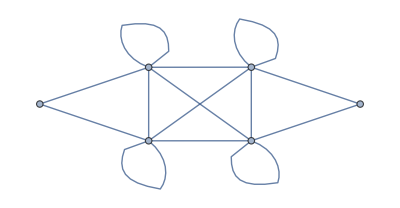

```mathematica
SetDirectory["~/Documents/UNH/Research/code/github/graph_21b"];
graph = { 
{0,1,0,0,0,1},
{1,1,1,0,1,1},
{0,1,1,1,1,1},
{0,0,1,0,1,0},
{0,1,1,1,1,1},
{1,1,1,0,1,1}
 };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
CGamma = { 
{0,aa,0,0,0,bb},
{cc,dd,ee,0,ff,gg},
{0,hh,ii,jj,kk,ll},
{0,0,mm,0,nn,0},
{0,oo,pp,qq,rr,ss},
{tt,uu,vv,0,ww,xx}
};
level=4;
q=Exp[Pi*I/(3*(4+level))]; (* see physics paper *)
```